```mathematica
link=Install[LinkConnect["35135@192.168.217.129,33307@192.168.217.129",LinkProtocol->"TCPIP"]]
```

LinkObject[…]

```mathematica
handle = With[
{c=15,Ωp=1.0,Ωhe=1/4,Ωe=-100,θr=0.45,θe=Sqrt[0.8],θbp=0.045,θbhe=0.0225,ωbp=15*Sqrt[0.5],ωbhe=7.5*Sqrt[0.4],ωe=150,
ωp ={0.0266,
0.1207,
0.3312,
0.5934,
0.8158,
0.9859,
1.1178,
1.2203,
1.2975,
1.3516,
1.3836,
1.3943,
1.3836,
1.3516,
1.2975,
1.2203,
1.1178,
0.9859,
0.8158,
0.5934,
0.3312,
0.1207,
0.0266},
vd={1.90288,1.99424,2.025,1.99424,1.90288,1.7537,1.55124,1.30164,1.0125,0.692591,0.351638,0,-0.351638,-0.692591,-1.0125,-1.30164,-1.55124,-1.7537,-1.90288,-1.99424,-2.025,-1.99424,-1.90288},
vr={-0.692591,-0.351638,0,0.351638,0.692591,1.0125,1.30164,1.55124,1.7537,1.90288,1.99424,2.025,1.99424,1.90288,1.7537,1.55124,1.30164,1.0125,0.692591,0.351638,0,-0.351638,-0.692591}
},
dist=Join[
Thread[wstpDRingDistribution[Ωp,ωp,θr,θr,vd*2.25/2.025,vr*2.25/2.025]],
Thread[wstpDMaxwellianDistribution[{Ωp,Ωe,Ωhe},{ωbp,ωe,ωbhe},{θbp,θe,θbhe}]]];
wstpDCreateDispersionObject[c,dist]];
```

```mathematica
check=With[{k=2.6,wna=89Degree},wstpDFindRoot[handle,k Cos[wna],k Sin[wna],Complex[2.0,0.01] (1+0.0001 I {0,1,2}),MaxIterations->100]];
```

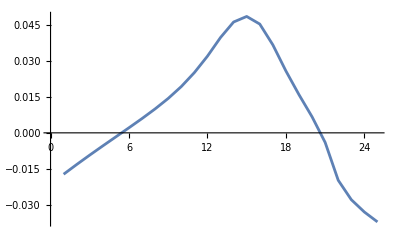

```mathematica
sol1=With[{k=Range[2.2,1.8,-0.05],wna=88.6Degree},wstpDFindRoot[handle,k Cos[wna],k Sin[wna],Complex[2.0,0.05] (1+0.0001 I {0,1,2}),MaxIterations->100]];
sol2=With[{k=Range[2.25,3.0,0.05],wna=88.6Degree},wstpDFindRoot[handle,k Cos[wna],k Sin[wna],Complex[2.0,0.05] (1+0.0001 I {0,1,2}),MaxIterations->100]];
sol1=Reverse[sol1[[2,2]]];
sol=Join[sol1,sol2[[2,2]]];
ListLinePlot[Im[sol]]
```

```mathematica
Export["vs=2.25,87.6,0.5h0.4he-0.045-im-5,9.2-12.0.csv",Im[sol]];

Export["vs=2.25,87.6,0.5h0.4he-0.045-re-5,9.2-12.0.csv",Re[sol]];
```

```mathematica
r=Complex[2.0,0.05] ;
dk=0.05;
kl=1.8;
kmid=2.2;
kr=3.0;
dwna=0.2Degree;
wnai=87Degree;
wnamid=88.6Degree;
wnaf=89Degree;
a2={};
With[{k=Range[kmid,kl,-dk]},Do[sol=wstpDFindRoot[handle,k Cos[wna],k Sin[wna],r(1+0.0001 I {0,1,2}),MaxIterations->100];
a2=Append[a2,Im[sol[[2,2]]]],{wna,wnamid,wnaf,dwna}]];
a1={};
With[{k=Range[kmid+dk,kr,dk]},Do[sol=wstpDFindRoot[handle,k Cos[wna],k Sin[wna],r (1+0.0001 I {0,1,2}),MaxIterations->100];
a1=Append[a1,Im[sol[[2,2]]]],{wna,wnamid,wnaf,dwna}]];
a3={};
With[{k=Range[kmid,kl,-dk]},Do[sol=wstpDFindRoot[handle,k Cos[wna],k Sin[wna],r (1+0.0001 I {0,1,2}),MaxIterations->100];
a3=Append[a3,Im[sol[[2,2]]]],{wna,wnamid-dwna,wnai,-dwna}]];
a4={};
With[{k=Range[kmid+dk,kr,dk]},Do[sol=wstpDFindRoot[handle,k Cos[wna],k Sin[wna],r(1+0.0001 I {0,1,2}),MaxIterations->100];
a4=Append[a4,Im[sol[[2,2]]]],{wna,wnamid-dwna,wnai,-dwna}]];
```

```mathematica
ra2=Map[Reverse,a2];
a1;
toup=Join[ra2,a1,2];
ra3=Map[Reverse,a3];
a4;
todown=Join[ra3,a4,2];
rtodown=Reverse[todown];
```

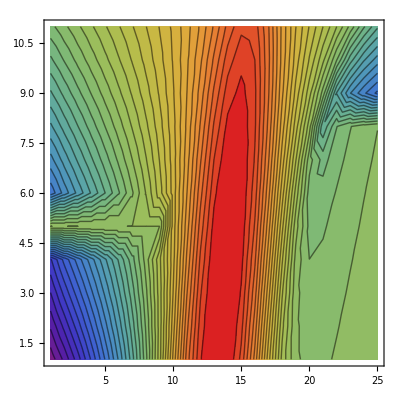

0.0519622

{{4,14}}

```mathematica
total=Join[rtodown,toup];
 ListContourPlot[total,ColorFunction->"Rainbow",Contours->40]
Export["vs=2.25-0.9h-0.045-2.8-3.0,86.8-89.5-.csv",total];
Max[total]
Position[total,Max[total]]
```

```mathematica
total
```

{{-0.0260567,-0.0139539,-0.000689704,0.0159908,0.040202,0.0623091,0.0599222,0.0149751,0.00360349,-0.00110697,-0.00166222,-0.00131386,-0.000849958},{-0.0205651,-0.00959582,0.00229834,0.0170204,0.0385859,0.0613818,0.0619997,0.0496522,0.0393758,0.0174897,-0.0013065,-0.0131482,-0.0215516},{-0.0152959,-0.00546405,0.00510918,0.0180133,0.0369098,0.0599048,0.0635097,0.0505325,0.0374495,0.0150589,-0.00102395,-0.0109695,-0.0181105},{-0.0102031,-0.00164105,0.00765364,0.0188609,0.0351244,0.0577336,0.0642864,0.0512696,0.0348972,0.0131094,-0.000328845,-0.0085943,-0.0145823},{-0.0052543,0.00175948,0.00982141,0.0194308,0.0331257,0.0546613,0.0641262,0.0516709,0.031711,0.0116267,0.000632555,-0.00612476,-0.011045}}